## Parameterized Numerical Fit For Geza

```mathematica
OS="win";(*or,linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",descDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\daq-tools-bkg-auto\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\Pictures\\nstar\\runs2"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="\\";
];
If[OS=="axion",
Print["Working Directory: ",descDir="/home/prajwal/Dropbox/nEDM/daq-tools-bkg-auto/nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["/home/prajwal/Dropbox/Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="/home/prajwal/Dropbox/nEDM/Pictures/nstar/runs"];Print["(SysDir) System Directory: ",SysDir="/home/prajwal/Dropbox/nEDM/system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="/";
];
metaStructure={Real,Word,Real,Real,Real,Real,Real};
metaStructure2={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
```

Working Directory: C:\Users\Prajwal\Dropbox\nEDM\daq-tools-bkg-auto\nstar_online

(AscDir) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\rawdata

SetDirectory::cdir: Cannot set current directory to C:\Users\Prajwal\Dropbox\Scratch.

(ScrDir) Scratch Directory: $Failed

(PicDir) Picture Directory: C:\Users\Prajwal\Dropbox\nEDM\Pictures\nstar\runs2

(SysDir) System Directory: C:\Users\Prajwal\Dropbox\nEDM\system

Rawdata on mpc1636:/xdata/nedm_data/RawData

## Check

```mathematica
Clear[en,iScale,iAlpha,iBeta,iEpeak,iW,iEta,iX]
EnergySpectrumDecay[en_,iScale_,iAlpha_,iBeta_,iEpeak_,iW_,iEta_,iX_]:=en^iAlpha*(1-Exp[-(165-en)/iBeta])/(1+Exp[(en-iEpeak)/iW])*iScale*Exp[-iX/885]*Exp[-iX*2*(1/(en/185)*ArcSin[Sqrt[(en/185)]]-Sqrt[1/(en/185)-1])*iEta*Sqrt[en/5.227]/0.15887];
EnergySpectrumDecay[en,iScale,iAlpha,iBeta,iEpeak,iW,iEta,iX]
```

(ⅇ^(-iX/885-5.50633 √en iEta iX (-√(-1+185/en)+(185 ArcSin[(√en)/(√185)])/en)) (1-ⅇ^((-165+en)/iBeta)) en^iAlpha iScale)/(1+ⅇ^((en-iEpeak)/iW))

```mathematica
pt[x_]:=Integrate[EnergySpectrumDecay[en,1,.5,50,50,50,0.0003,x],{en,0,165}];
```

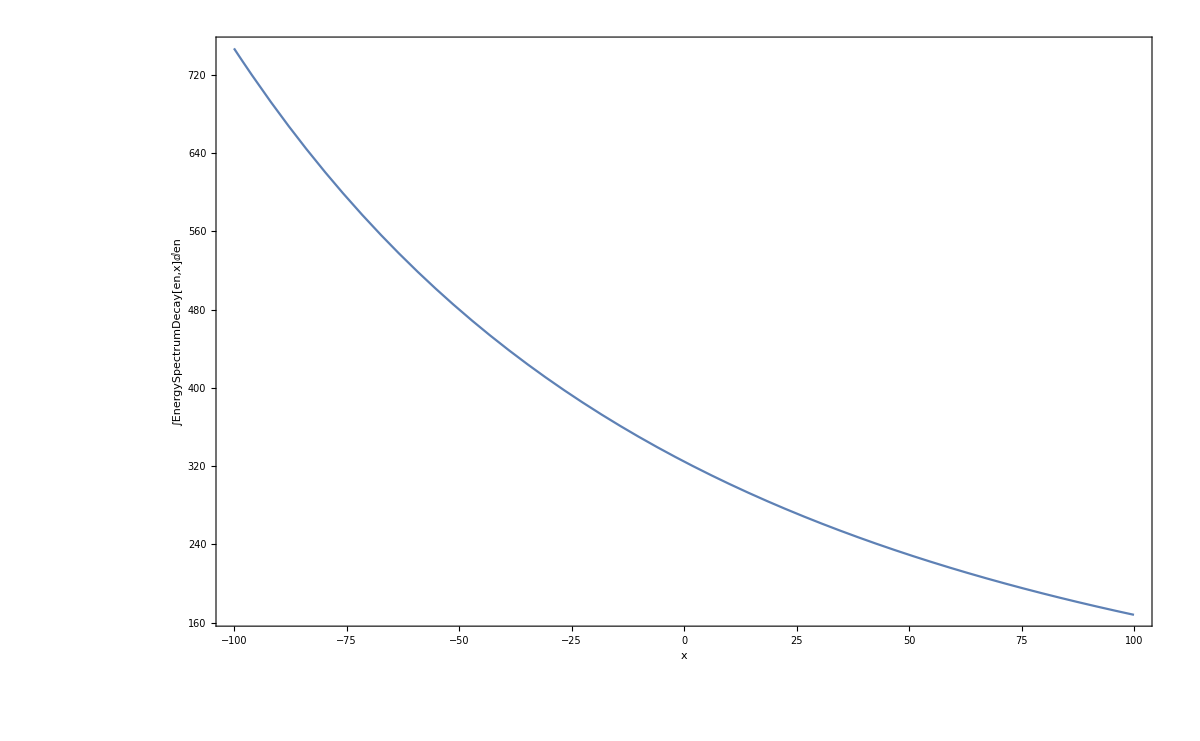

```mathematica
Plot[pt[x],{x,-100,100},ImageSize->1200,Frame->True,FrameLabel->{"x","∫EnergySpectrumDecay[en,x]ⅆen"}]
```

```mathematica
pt[x]
```

## Function Definitions

```mathematica
Clear[t,p,tau,e,a,b,c,v,ep,w]
emin=1;
emax=2;
fitsampledata=Table[{t,N[10 Exp[-t/100]]},{t,0,100,1}];
p[e_?NumericQ,a_?NumericQ,b_?NumericQ,v_?NumericQ,ep_?NumericQ,w_?NumericQ]:=(e^a(v-e)^b)/(1+Exp[(e-ep)/w]);
tau[c_?NumericQ,e_?NumericQ,v_?NumericQ]:=c/(√e(v/e ArcSin[√(e/v)]));
f[t_?NumericQ,a_?NumericQ,b_?NumericQ,v_?NumericQ,ep_?NumericQ,w_?NumericQ,c_?NumericQ]:=NIntegrate[p[e,a,b,v,ep,w]Exp[-t/tau[c,e,v]],{e,emin,emax}];
```

```mathematica
NonlinearModelFit[fitsampledata,
{f[t,afit,bfit,vfit,epfit,wfit,cfit],
{afit>1,bfit>1,vfit>3,epfit>0,epfit<1,wfit>1,cfit>1}
},
{{afit,1},{bfit,1},{vfit,2},{epfit,1},{wfit,1},{cfit,1}},
t]
```

## Test-Area

```mathematica
Clear[t,p,tau,e,a,b,c,v,ep,w]
emin=1;
emax=10;
fitsampledata=Table[{t,N[10 Exp[-t/100]]},{t,0,100,1}];
p[e_?NumericQ,a_?NumericQ,b_?NumericQ,v_?NumericQ,ep_?NumericQ,w_?NumericQ]:=e+a+b+v+ep+w;
tau[c_?NumericQ,e_?NumericQ,v_?NumericQ]:=c+e+v;
f[t_?NumericQ,a_?NumericQ,b_?NumericQ,v_?NumericQ,ep_?NumericQ,w_?NumericQ,c_?NumericQ]:=NIntegrate[p[e,a,b,v,ep,w]tau[c,e,v],{e,emax,emin}];
NonlinearModelFit[fitsampledata,f[t,afit,bfit,vfit,epfit,wfit,cfit],{{afit,1},{bfit,1},{vfit,1},{epfit,1},{wfit,1},{cfit,1}},t]
%["ParameterTable"]
```

FittedModel[f[t,-12.9316,-7.23565,9.06383,8.4489,-4.19651,-9.04744]]

| Estimate | Standard Error | t-Statistic | P-Value
afit | -12.9316 | 0.000816349 | -15840.8 | 7.49808×10^-307
bfit | -7.23565 | 0.000816349 | -8863.43 | 6.78602×10^-283
vfit | 9.06383 | 0.000616412 | 14704.2 | 8.84922×10^-304
epfit | 8.4489 | 0.000816349 | 10349.6 | 2.72873×10^-289
wfit | -4.19651 | 0.000816349 | -5140.59 | 2.02999×10^-260
cfit | -9.04744 | 0.000199937 | -45251.5 | 3.7042302204972×10^-350

```mathematica
Clear[t,p,tau,e,a,b,c,v,ep,w]
emin=1;
emax=2;
fitsampledata=Table[{t,N[10 Exp[-t/100]]},{t,0,100,1}];
p[e_?NumericQ,a_?NumericQ,b_?NumericQ,v_?NumericQ,ep_?NumericQ,w_?NumericQ]:=(e^a(v-e)^b)/(1+Exp[(e-ep)/w]);
tau[c_?NumericQ,e_?NumericQ,v_?NumericQ]:=c+e+v;
f[t_?NumericQ,a_?NumericQ,b_?NumericQ,v_?NumericQ,ep_?NumericQ,w_?NumericQ,c_?NumericQ]:=NIntegrate[p[e,a,b,v,ep,w]tau[c,e,v],{e,emax,emin}];
NonlinearModelFit[fitsampledata,
{f[t,afit,bfit,vfit,epfit,wfit,cfit],
{afit>1,bfit>1,vfit>3,epfit>0,epfit<1,wfit>1,cfit>1}
},
{{afit,1},{bfit,1},{vfit,1},{epfit,1},{wfit,1},{cfit,1}},
t,
Method->NMinimize]
%["ParameterTable"]
```

NonlinearModelFit::sdir: Search direction has become too small.

FittedModel[f[t,1.,1.,3.,0.,1.,1.]]

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
afit | 1. | 0.0462471 | 21.623 | 1.8211×10^-38
bfit | 1. | 0.0552909 | 18.0861 | 1.58575×10^-32
vfit | 3. | 0.111897 | 26.8103 | 4.27293×10^-46
epfit | 0. | 0.105829 | 0. | 1.
wfit | 1. | 0.154965 | 6.45306 | 4.5909×10^-9
cfit | 1. | 0.0241517 | 41.405 | 1.35722×10^-62

```mathematica
xx=3.03
f[1,2,2,xx,xx,xx,xx]
```

3.03

826785.+78160.5 ⅈ

```mathematica
-1^1.1
```

-1.